```mathematica
ClearAll["Global`*"]
```

```mathematica
(* Set the notebook directory to the local directory *)
SetDirectory[NotebookDirectory[]];
(* Check that this is the directory *)
NotebookDirectory[]
```

## Overview of the program

```mathematica
(* 



This notebook computes the "quasinormal modes" associated with perturbations of holographic superconductors. This simple example illustrates a few numerical techniques including pseudospectral methods to solve differential equations as well as finding eigenvalues. This is a version of the numerics in https://arxiv.org/pdf/2212.10410 which rescales the U(1) gauge field Subscript[A, M]->Subscript[A, M]/Q and the complex scalar field ψ->Subscript[ψ, M]/Q with Q->∞. In this limit, the spacetime is fixed and only the matter fields have non-trivial behavior. This is equivalent to suppressing energy and momentum fluctuations in the superconductor and only allowing charge fluctuations. The hydrodynamic modes ω(k) can be matched exactly including both real and imaginary parts in the limit k<<1, however for the sake of readability, I will only match the velocity of the second sound mode: lim_(k->0) ω(k). To obtain the imaginary components, one needs the low frequency response functions and then uses Kubo formulae--the numerical techniques for these are very similar to what is shown here, so I have omitted this step. If you would like to see how that works, let me know and I will append it to the program.



*)

(*



There are five main parts to the program which can each be run independently or the whole notebook can be run from the top. 

1.) In the first part we derive the equations of motion describing holographic superconductors in equilibrium and then subject to a linearized perturbation.  

2.) In the second part we solve the equations of motion for the background solution. The asymptotic behavior of these solutions defines sources and expectation values for the electric current <J^μ> and the order parameter <ψ^*ψ> . This is a boundary value problem for a coupled set of ordinary differential equations.

3.) In the third part we solve the linearized equations of subject to the boundary condition that the sources vanish. Since response functions are formally given by Subscript[G^R, OO](ω,k) = (δ<O>)/Subscript[δs, O] where Subscript[s, O] is the source for the operators <O>, solutions to these equations give the poles of the response functions. They exist at limited values of ω(k) which define the dispersion relations of hydrodynamic fluctuations in a superconductor. Numerically, this means that we must find the ω(k), i.e. we solve an eigenvalue problem. The matrices are dense so there is no way to make diagonalization faster and Mathematica's built in eigensolver is sufficiently efficient. However, in step 4, we illustrate a way to isolate an individual eigenvalue and increase precision and accuracy. 

4.)We show how to efficiently increase accuracy for a single eigenvalue.

5.) Finally, we compare to the predictions of the hydrodynamic theory and show that the results agree. 





*)
```

```mathematica
(* More details on part 2.

 To solve the ODEs, we will use a version of Newton's method. The essential idea is that we have an equation we want to solve, which we may write Subscript[E, j][S^i] = 0 for some configuration of the fields S^i, but we are at a different value X^i(t=0). As with Newton's method of root finding, from step t to step t+1, we choose the next X^i(t+1) such that Subscript[E, j]'[X^i(t)](X^i(t+1)-X^i(t)) = -Subscript[E, j][X^i(t)]. The fields X^i are a vector so this can be solved with built in linear algebra tools. 

Mathematica is competitive with other programming languages for linear algebra, see https://reference.wolfram.com/language/tutorial/LinearAlgebraInMathematicaOverview.html.

 At each step, then, we solve M^ij(t)δX^j(t)=-E^i(t) with M^ij(t) = δE^i/δX^j(t) until we reach a point where δX^i is below some threshold. 
*)
```

```mathematica
(* More details on part 3.


The linearized equations of motion have the form ∑_n ω^n Subscript[C^i, j](n)δX^j = 0, where Subscript[C^i, j] are differential operators (that include the boundary conditions) acting on the linearized fields δX^j and ω is the frequency of the plane wave perturbation. A simple example which has only one power of ω can be written,

Subscript[C^i, j](0)δX^j=-Subscript[ωC^i, j](1)δX^j,

which has the form of a generalized eigenvalue problem with matrices Subscript[C^i, j](0) and -Subscript[C^i, j](1). Generalized eigenvalue equations can be solved efficiently with Mathematica. When there are more powers of ω, the equations still have the form of a generalized eigenvalue problem, but in terms of a modified eigenvector. For instance, if the largest power of ω is 2, then,

({{Subscript[C^i, j](1), Subscript[C^i, j](0)}, {-I, 0}})({{ωδX}, {δX}})=-ω({{Subscript[C^i, j](2), 0}, {0, I}})({{ωδX}, {δX}}) ,

returns the same linearized equation but increases the size of the matrices by a power of 4. If higher powers of ω appeared we would continue this process,

({{Subscript[C^i, j](nmax-1), Subscript[C^i, j](nmax-2), ..., Subscript[C^i, j](0)}, {-I, 0, ..., 0}, {-, -I, ..., 0}, {0, 0, ..., 0}})({{ω^(n-1)δX}, {ω^(n-2)δX}, {...}, {δX}})=-ω({{Subscript[C^i, j](nmax), 0, ..., 0}, {0, I, ..., 0}, {0, 0, ..., 0}, {0, 0, ..., I}})({{ω^(n-1)δX}, {ω^(n-2)δX}, {...}, {δX}}).


*)
```

```mathematica
(* More details on part 4. 

In part 4, we increase the grid size to get better accuracy. However, this drastically increases the size of the matrices we would need to diagonalize. In general, we care about only the lowest lying eigenvalues, so diagonalizing the full matrix is overkill. The most efficient route is to promote ω to a function of z, ω->ω[z], with an equation of motion ω'[z] = 0, and then use Newton-Raphson. When we do this, it is important to fix a normalization for the eigenvector,though the choice is arbitrary. We will choose that the linearized fields sum to one on the horizon. 

*)
```

```mathematica
(* Other notes: There are ways to optimize these types of programs via compiled functions which can include arbitrary precision computations. However, these tend to slightly increase overhead for the problem presented here so instead I just construct the numerical versions of the differential equations using replacement rules which resulted in a more efficient and readable code for this problem. *)
```

## 1.) Deriving the equations of motion

### Define metric

```mathematica
(* The background is fixed but can be chosen by hand. A natural choice in the probe limit is AdS-Schwarzschild with f[z] = 1-(z/zh)^d in Subscript[AdS, d+1] with Anti de Sitter length scale set to 1.  It is simple to write the equations in general dimension, but for the sake of simplicity, I fix d = 3. This describes a holographic superconductor in 2 spatial and 1 time dimension. *)
```

```mathematica
$Assumptions={ϕ[z]≥0,ψ[z]≥0,f[z]≥0,1≥z≥0,η[z]≥0};
(* coordinate variables. t is time, z is AdS radial direction, x and y are coordinates on constant t and z slices *)
coord = {t,z,x,y};
dcoord = {dt, dz, dx, dy};
dim=Length[coord];
(* The line element ds^2 for the background *)
ds2 =1/z^2(-f[z] dt^2+dz^2/f[z]+(dx^2+dy^2));
G = Table[If[i==j,Coefficient[ds2,dcoord[[i]]^2],(1/2)Coefficient[ds2,dcoord[[i]]*dcoord[[j]]]],{i,1,dim},{j,1,dim}];
rootDetG =√(-Det[G]);
Ginv = Inverse[G];
```

### Define Lagrangian

```mathematica
(*First define the charged scalars *)
Ψ=ψ[t,z,x,y];
Ψs=ψs[t,z,x,y];
(* Define U(1) gauge field and U(1) field strength *)
Amax = {at[t,z,x,y],az[t,z,x,y],ax[t,z,x,y],ay[t,z,x,y]};
Fab = Table[D[Amax[[a]],coord[[b]]]-D[Amax[[b]],coord[[a]]],{a,1,dim},{b,1,dim}];
(* Define potential for charged scalar *)
V[psi_,psistar_]:= -(dim-1)(dim-2)-2psi*psistar;
(* Define lagrangian, L = √-g(-1/4 Subscript[F, MN] F^MN - (∂_M -Subscript[iQA, M])ψ(∂^M +iQA^M)ψ^*). We write ψ[z] = η[z]e^iα[z]. It is consistent to set α=0, so that ψ^*= ψ. The Q here is the charge of the scalar after the probe limit rescaling. It can be different than Q=1, though for simplicity we will choose Q = 1. *)
Lag = rootDetG(-(1/4)Sum[Fab[[a,b]]Fab[[c,e]]Ginv[[a,c]]Ginv[[b,e]],{a,1,dim},{b,1,dim},{c,1,dim},{e,1,dim}] - V[Ψ,Ψs]-Sum[Ginv[[a,b]]((1/2)((D[Ψ,coord[[a]]]-I*Q*Amax[[a]]Ψ)(D[Ψs,coord[[b]]]+I*Q*Amax[[b]]Ψs)+(D[Ψ,coord[[b]]]-I*Q*Amax[[b]]Ψ)(D[Ψs,coord[[a]]]+I*Q*Amax[[a]]Ψs))),{a,1,dim},{b,1,dim}]);
```

### Equations of motion

```mathematica
(* Perturb the background with plane waves. For the background, it is consistent to set ψ=ψ^*=η. It is conventional to name At = ϕ[z] for the background solution. *)
linearRepRulesa={
at[t,z,x,y]->ϕ[z]+ϵs*at[z]*Exp[-I*(ω*t-kk*x)],
ax[t,z,x,y]->Ax[z]+ϵs*ax[z]Exp[-I*(ω*t-kk*x)],
ay[t,z,x,y]->ϵs*ay[z]Exp[-I*(ω*t-kk*x)],
ψ[t,z,x,y]->η[z]+ϵs*(σr[z]+I*σi[z])Exp[-I*(ω*t-kk*x)],
ψs[t,z,x,y]->η[z]+ϵs*(σr[z]-I*σi[z])Exp[-I*(ω*t-kk*x)],
az[t,z,x,y]->0};
(* Define derivatives *)
linearRepRules= Flatten[{linearRepRulesa,Table[D[linearRepRulesa,coord[[a]]],{a,1,dim}],Table[D[D[linearRepRulesa,coord[[a]]],coord[[b]]],{a,1,dim},{b,1,dim}]}];
Clear[linearRepRulesa]
```

```mathematica
(* Derive the equations of motion through linearization (different linearization than above) *)
```

```mathematica
δAmax =  {δat[t,z,x,y],δax[t,z,x,y],δay[t,z,x,y],δaz[t,z,x,y]};
dLag = D[Lag/.Flatten[{ψ[t,z,x,y]->ψ[t,z,x,y]+ϵ*δψ[t,z,x,y],ψs[t,z,x,y]->ψs[t,z,x,y]+ϵ*δψs[t,z,x,y],Table[D[{ψ[t,z,x,y]->ψ[t,z,x,y]+ϵ*δψ[t,z,x,y],ψs[t,z,x,y]->ψs[t,z,x,y]+ϵ*δψs[t,z,x,y]},coord[[j]]],{j,1,dim}],Table[{Amax[[i]]->Amax[[i]]+ϵ*δAmax[[i]],Table[D[Amax[[i]]->Amax[[i]]+ϵ*δAmax[[i]],coord[[j]]],{j,1,dim}]},{i,1,dim}]}],ϵ]/.{ϵ->0};
```

```mathematica
MaxEQ=Table[Simplify[1/rootDetG(Sum[D[D[dLag,D[δAmax[[j]],coord[[i]]]],coord[[i]]],{i,1,dim}]-D[dLag,δAmax[[j]]])/.linearRepRules],{j,1,dim}];
MaxEQ0=MaxEQ/.{ϵs->0}//Together//Numerator//Simplify;
MaxEQ1=ⅇ^(-ⅈ (kk x-t ω)) D[MaxEQ,ϵs]/.{ϵs->0}//Together//Numerator//Simplify;
Clear[δAmax]
```

```mathematica
ψeq =Simplify[ 1/rootDetG(Sum[D[D[dLag,D[δψs[t,z,x,y],coord[[a]]]],coord[[a]]],{a,1,dim}]-D[dLag,δψs[t,z,x,y]])/.linearRepRules];
ψseq =Simplify[1/rootDetG (Sum[D[D[dLag,D[δψ[t,z,x,y],coord[[a]]]],coord[[a]]],{a,1,dim}]-D[dLag,δψ[t,z,x,y]])/.linearRepRules];
```

```mathematica
ψeq0=ψeq/.{ϵs->0}//Together//Numerator//Simplify;
ψseq0=ψseq/.{ϵs->0}//Together//Numerator//Simplify;
ψeq1=ⅇ^(-ⅈ kk x)D[ψeq,ϵs]/.{ϵs->0}//Together//Numerator//Simplify;
ψseq1=ⅇ^(-ⅈ kk x)D[ψseq,ϵs]/.{ϵs->0}//Together//Numerator//Simplify;
```

```mathematica
(* Check that ψ = ψ^* in the background *)
```

```mathematica
ψeq0-ψseq0//Simplify
```

0

```mathematica
(* It is useful to algebraically solve ψeq1 and ψseq1 for σi'' and σr'' giving simpler eq's.*)
```

```mathematica
σiσrpp = Flatten[Solve[{ψeq1==0,ψseq1==0},{σr''[z],σi''[z]},Assumptions->{}]];
```

```mathematica
σieq=σi''[z]-(σi''[z]/.σiσrpp)//Together//Numerator//Simplify;
σreq=σr''[z]-(σr''[z]/.σiσrpp)//Together//Numerator//Simplify;
Clear[σiσrpp,ψeq1,ψseq1]
```

```mathematica
(* Check that ay[z] decouples*)
```

```mathematica
MaxEQ1[[4]]/.{ay[z]->0,ay'[z]->0,ay''[z]->0}
```

0

```mathematica
(* There is also a gauge constraint from the z equation. We can include this as a boundary condition in our numerics. *)
```

```mathematica
MaxEQ1[[2]]
```

ⅈ z^4 ω at'[z]+z^2 f[z] (ⅈ kk z^2 ax'[z]+2 Q σi[z] η'[z]-2 Q η[z] σi'[z])

```mathematica
backgroundEQs = {ψeq0,MaxEQ0[[1]],MaxEQ0[[3]]};
linearizedEQs={MaxEQ1[[1]],MaxEQ1[[3]],σreq,σieq,MaxEQ1[[2]]}/.{ay[z]->0,ay'[z]->0,ay''[z]->0};
```

```mathematica
(* Check if linearized e.o.m.'s can be simplified using background e.o.m.'s *)
```

```mathematica
Table[Coefficient[linearizedEQs[[i]],{ϕ''[z],η''[z],Ax''[z]}],{i,1,Length[linearizedEQs]}]
```

{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}

```mathematica
Export[NotebookDirectory[]<>"EQs/probe_4d_backgroundEQs.mx",backgroundEQs];
Export[NotebookDirectory[]<>"EQs/probe_4d_linearizedEQs.mx",linearizedEQs];
```

```mathematica
Clear[coord, dcoord, dim, ds2, G, Ginv, rootDetG, Lag, Ψ, Ψs, Amax, Fab, V,dLag,MaxEQ,MaxEQ0,MaxEQ1,ψeq,ψseq,ψeq0,ψseq0,ψeq1,ψseq1,linearRepRules,σieq,σreq]
```

```mathematica
(* via the holographic dictionary, retarded response functions are obtained via "ingoing boundary conditions" with a fluctuation X[z]->Subscript[X, h] e^(iωv(z)) where +v is the "ingoing" and -v is outgoing tortoise coordinate. For Schwarzschild, v[z] = -log(1-z)/3. *)
```

```mathematica
sn=-1;
```

```mathematica
ingoingrulesa=Flatten[{
ax[z]->ax[z](Exp[sn*I*ω*(Log[1-z]/3)]),
at[z]->at[z](Exp[sn*I*ω*(Log[1-z]/3)]),
σi[z]->σi[z](Exp[sn*I*ω*(Log[1-z]/3)]),
σr[z]->σr[z](Exp[sn*I*ω*(Log[1-z]/3)])
}];
ingoingrules=Flatten[{ingoingrulesa,D[ingoingrulesa,z],D[ingoingrulesa,{z,2}]}];
```

```mathematica
ingoingEQs= Expand[(9/((1-z)^((ⅈ sn ω)/3) ))(linearizedEQs/.ingoingrules)]//Simplify//Together//Numerator//Simplify;
```

```mathematica
Export[NotebookDirectory[]<>"EQs/probe_4d_ingoingEQs.mx",ingoingEQs];
```

```mathematica
Clear[ingoingrulesa,ingoingrules,linearizedEQs,ingoingEQs]
```

## 2.) Background field configurations via Newton-Raphson

```mathematica
Clear[μ,μs]
```

### Numerical Parameters

```mathematica
(* Often, higher than double floating precision is necessary for finding accurate eigenvalues, since we perturb around a numerical solution. Mathematica handles this well with arbitrary precision computation. Here, we fix precision to 60 significant digits. *)
```

```mathematica
mp=60;
$MinPrecision=mp;
```

```mathematica
(* It can speed up the calculation to set very small numbers to zero. We will pick a number < 10^-mp but still small *)
```

```mathematica
chopmin=10^-100;
```

```mathematica
(* Define number of grid points and min and max values. There is a minimum size for the coarse grid to get accurate eigenvalues. Something above around 40 should be good.*)
```

```mathematica
NumGridPoints =40; 
{zmin, zmax} = {0,1};
```

```mathematica
(* Choose a value for the charge of the complex scalar, Q.*)
```

```mathematica
Q=1;
```

```mathematica
(* Choose parameters for the family of background solutions *)
```

```mathematica
Nμ=10;
Nμs=10;
(* Choose a min and max for the potentials. Spontaneous symmetry breaking requires μ ~ 4  when Q = 1*)
{μmin,μmax} = {5,6};
{μsmin,μsmax}={10^-6,1/3};
```

### Define Chebyshev grid and derivative matrices

```mathematica
(* grid points z -> λ *)
λdata =N[Table[(zmax+zmin)/2-(zmax-zmin)/2*Cos[π*j/NumGridPoints],{j,0,NumGridPoints}],mp];(*Chebyshev Table*)
aλ=N[Table[Product[If[j==k,1,(λdata⟦j⟧-λdata⟦k⟧)],{k,1,NumGridPoints+1}],{j,NumGridPoints+1}],mp];
D1λ=Table[If[i==j,Sum[If[k==j,0,1/(λdata⟦j⟧-λdata⟦k⟧)],{k,1,NumGridPoints+1}],aλ⟦i⟧/(aλ⟦j⟧(λdata⟦i⟧-λdata⟦j⟧))],{i,1,NumGridPoints+1},{j,1,NumGridPoints+1}];
Clear[aλ];
D2λ=D1λ.D1λ;
D0λ = IdentityMatrix[NumGridPoints+1];
Drmatrices={D2λ,D1λ,D0λ};
(* test to check derivatives *)
Max[Table[3 λdata[[i]]^2,{i,1,NumGridPoints+1}]-D1λ.Table[λdata[[i]]^3,{i,1,NumGridPoints+1}]//Chop]
Max[Table[6λdata[[i]],{i,1,NumGridPoints+1}]-D2λ.Table[λdata[[i]]^3,{i,1,NumGridPoints+1}]//Chop]
```

0

0

### Initialize EQs

```mathematica
(* 

Boundary conditions in the UV(z=0) are Subscript[A, t][0]=μ+..., Subscript[A, x]=Subscript[μ, s]+..., η->z^2 Subscript[η, 0]+z^4 Subscript[η, 1]+... Furthermore, we use f[z] = 1-z^3. It is simpler to rescale the functions to impose these boundary conditions as Dirichlet. However, Subscript[η, 0] is the order parameter, so we don't want to fix this and μ. Instead, we will let this be a free parameter. At the horizon (z=1) Subscript[A, t] must vanish, otherwise Subscript[A, M] A^M would diverge.

*)
```

```mathematica
fieldredefa={η[z]->z^2*η[z],ϕ[z]->ϕ[z](1-z),f[z]->1-z^3};
fieldredef=Flatten[{fieldredefa,D[fieldredefa,z],D[fieldredefa,{z,2}]}];
Clear[fieldredefa]
```

```mathematica
(* Can import backgroundEQs here, if you don't want to run the first section *)
```

```mathematica
backgroundEQs = Import[NotebookDirectory[]<>"EQs/probe_4d_backgroundEQs.mx"]/.fieldredef//Expand//Simplify;
Clear[fieldredef]
```

```mathematica
(*Things are better behaved if we make sure to leading order, the equations are well defined at the boundary *)
```

```mathematica
Series[backgroundEQs,{z,0,-1}]//Simplify
Series[backgroundEQs/.{z->1-z},{z,0,-1}]//Simplify
```

{O[z]^3,O[z]^4,O[z]^4}

{O[z]^1,O[z]^1,O[z]^0}

```mathematica
EQs=({backgroundEQs[[1]]/(z^3(1-z)),backgroundEQs[[2]]/(z^4(1-z)),backgroundEQs[[3]]/z^4})//Expand//Simplify//PowerExpand//Simplify;
```

```mathematica
(* Once we have extracted the asymptotics, the remaining boundary conditions are smoothness *)
```

```mathematica
{bc1,bc2,bc3}=EQs/.{z->1}//Simplify;
```

```mathematica
BCs = {{η'[zmin],bc1},{ϕ[zmin]-μ,bc2},{Ax[zmin]-μs,bc3}}//Simplify;
```

```mathematica
Clear[bc1,bc2,bc3,backgroundEQs]
```

### Linearize EQs

```mathematica
(* Setting up the Newton-Raphson equations*)
```

```mathematica
fieldRep = {η->η+ϵs*δη,ϕ->ϕ+ϵs*δϕ,Ax->Ax+ϵs*δAx};
linBackEQ = D[(EQs/.fieldRep), ϵs]/.ϵs->0;
linBackBC= D[(BCs/.fieldRep), ϵs]/.ϵs->0;
Clear[fieldRep];

linFieldList = {δη[z],δϕ[z],δAx[z]};
(*dlinFieldList⟦choose a function⟧⟦choose a derivative⟧*)
dlinFieldList= Table[{D[linFieldList[[fun]], z,z],D[linFieldList[[fun]], z],linFieldList[[fun]]},{fun,1,Length[linFieldList]}];
Clear[linFieldList]
(* must change argument for boundary conditions from z to zmin or zmax *)
boundrules= {z->zmin,z->zmax};
Do[linEQcoeffs[eq,fun,der] =D[linBackEQ⟦eq⟧,dlinFieldList⟦fun⟧⟦der⟧],{eq,1,Length[EQs]},{fun,1,Length[EQs]},{der,1,Length[dlinFieldList[[eq]]]}];
(*BCc⟦BC_i⟧⟦min or max⟧⟦choose a function⟧⟦derivative⟧*)
Do[linBCcoeffs[eq,bound,fun,der] =D[linBackBC⟦eq⟧⟦bound⟧, (dlinFieldList⟦fun⟧⟦der⟧/.boundrules⟦bound⟧)],{eq,1,Length[EQs]},{bound,1,2},{fun,1,Length[EQs]},{der,1,Length[dlinFieldList[[eq]]]}];
```

```mathematica
Clear[linBackBC,linBackEQ,dlinFieldList,boundrules]
```

### Ranges of μ and μ_s

```mathematica
(* We use Chebyshev grids for the thermodynamic parameters to make derivatives straightforward*)
```

```mathematica
μtab=N[Table[(μmax+μmin)/2-(μmax-μmin)/2*Cos[π*j/Nμ],{j,0,Nμ}],mp];
```

```mathematica
μstab=N[Table[(μsmax+μsmin)/2-(μsmax-μsmin)/2*Cos[π*j/Nμs],{j,0,Nμs}],mp];
```

```mathematica
ηvectab=Table[0,{i,1,Nμs+1},{j,1,Nμ+1}];
ϕvectab=Table[0,{i,1,Nμs+1},{j,1,Nμ+1}];
Axvectab=Table[0,{i,1,Nμs+1},{j,1,Nμ+1}];
```

### Seeds

```mathematica
(* Define starting seeds. These can also be imported from lower precision solutions. The seeds for Subscript[A, t] and Subscript[A, x] depend on the values of μ and Subscript[μ, s]. The seed for η will be updated throughout the algorithm because it is less stable. *)
```

```mathematica
ηseed= Table[15*(1-λdata[[i]]^2),{i,1,NumGridPoints+1}];
ϕseed=Table[μtab[[j]](1-λdata[[i]]),{j,1,Nμ+1},{i,1,NumGridPoints+1}];
Axseed= Table[μstab[[j]],{j,1,Nμs+1},{i,1,NumGridPoints+1}];
{ηvec,ϕvec,Axvec}={ηseed,ϕseed[[1]],Axseed[[1]]};
combinedFields = Flatten[{ηvec,ϕvec,Axvec}];
```

### Newton-Raphson loop

```mathematica
(* Define thresholds which will halt the evaluation if exceeded*)
```

```mathematica
Error =10^(-(mp/2));
ErrorMax = 1000000;
```

```mathematica
μcount=1;
μscount=1;
```

```mathematica
nb=CreateDocument["",WindowSize->{Scaled[1/5],Scaled[1/2]}];
While[μscount≤Nμs+1,

μcount=1;

μs=μstab[[μscount]];

{ηvec,ϕvec,Axvec}={ηseed,ϕseed[[μcount]],Axseed[[μscount]]};

(* Flatten fields into a single vector *)
combinedFields= Flatten[{ηvec,ϕvec,Axvec}];


While[μcount≤Nμ+1,

μ=μtab[[μcount]];

(* In case a previous solution flows to a zero solution for ψ, reinitiate the seed *)

ηvec=If[Max[Abs[ηvec]]<1/1000,ηseed,ηvec];

ϵp = (ErrorMax-Error)/2;
count = 0;

NotebookWrite[nb,Cell[BoxData@RowBox[{"μ_s # ", μscount,".) μ # ",μcount, ".) ",Timing[

While[ϵp>Error&&ϵp<ErrorMax,

(* rules for replacing functions in the equations *)
Do[coeffargs[i] = {z->λdata⟦i⟧,
ϕ''[z]->D2λ⟦i⟧.ϕvec,ϕ'[z]->D1λ⟦i⟧.ϕvec,ϕ[z]->ϕvec⟦i⟧,
Ax''[z]->D2λ⟦i⟧.Axvec,Ax'[z]->D1λ⟦i⟧.Axvec,Ax[z]->Axvec⟦i⟧,η''[z]->D2λ⟦i⟧.ηvec,η'[z]->D1λ⟦i⟧.ηvec,η[z]->ηvec⟦i⟧
},{i,1,NumGridPoints+1}];

(* Construct the derivative matrix *)
M =ArrayFlatten[Table[Sum[Flatten[Table[Piecewise[{{linBCcoeffs[m,1,n,dd]/.(coeffargs[1]/.{z->zmin}),i==1},
{linBCcoeffs[m,2,n,dd]/.(coeffargs[NumGridPoints+1]/.{z->zmax}),i==NumGridPoints+1},{linEQcoeffs[m,n,dd]/.coeffargs[i],i≠1&&i≠NumGridPoints+1}}],{i,1,NumGridPoints+1}]]Drmatrices[[dd]],{dd,1,Length[Drmatrices]}],{m,1,Length[EQs]},{n,1,Length[EQs]}]];

(* Construct the value of the eoms given the current configuration of the fields. *)
Etot =Chop[Flatten[Parallelize[Table[Piecewise[{{BCs[[m,1]]/.(coeffargs[1]/.{z->zmin}),i==1},{BCs[[m,2]]/.(coeffargs[NumGridPoints+1]/.{z->zmax}),i==NumGridPoints+1},{EQs[[m]]/.coeffargs[i],i≠1&&i≠NumGridPoints+1}}],
{m,1,Length[EQs]},{i,1,NumGridPoints+1}]]],chopmin];

(* Solve for the change in the fields *)
deltaFields=Chop[LinearSolve[M,-Etot],chopmin];

(* Compute the norm of deltaFields to keep track of convergence *)
ϵp=Norm[deltaFields,∞];

If[NumberQ[ϵp],NotebookWrite[nb,Cell[BoxData@RowBox[{"ϵp= ",ϵp}],"Output"]],Break[]];

(* If the norm is too large, introduce friction. *)
friction=If[ϵp<1,1,1/10];

combinedFields =combinedFields+friction*deltaFields;

(* partition the solution for the combined fields into individual fields *)
{ηvec,ϕvec,Axvec} = Partition[combinedFields,NumGridPoints+1];

Clear[friction,deltaFields];

count++;
];

]⟦1⟧,", # Iteration = ", count}],"Output"]];


(* update the ηseed *)
ηseed=If[μcount==1&&(100>Abs[Chop[ηvec[[1]]]]>0),ηvec,ηseed];

(* Can store the field values in memory*)
ηvectab[[μscount,μcount]]=ηvec;
ϕvectab[[μscount,μcount]]=ϕvec;
Axvectab[[μscount,μcount]]=Axvec;

μcount++;

];

μscount++;

];
NotebookClose[nb];
```

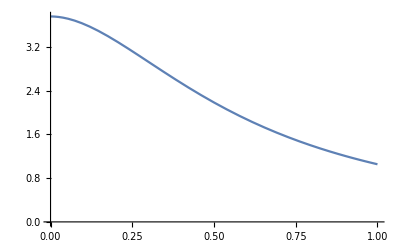

```mathematica
ListLinePlot[Table[{λdata[[i]],ηvectab[[1,1,i]]},{i,1,NumGridPoints+1}]]
```

```mathematica
(* Export solutions, include Chebyshev grid parameters so we don't duplicate efforts *)
```

```mathematica
Export[NotebookDirectory[]<>"Data/probe_background_4d_sols.mx",{Q,λdata,D0λ,D1λ,D2λ,μtab,μstab,ϕvectab,Axvectab,ηvectab}];
```

## 3.) Quasinormal modes or hydrodynamic spectrum

```mathematica
(* Make sure variables don't have any values stored in memory*)
```

```mathematica
Clear[kk,zmin,zmax]
```

### Numerical Parameters

```mathematica
(* If we start here, useful to redefine parameters for the numerics. Start with precision *)
```

```mathematica
{zmin,zmax}={0,1};
```

```mathematica
mp=60;
$MinPrecision=mp;
```

```mathematica
(* Set threshold for "0" < 10^-mp *)
```

```mathematica
chopmin=10^-100;
```

```mathematica
(* Define number of grid points and min and max values. Since we will need a background solution, here we import the solution. *)
```

```mathematica
{Q,λdata,D0λ,D1λ,D2λ,μtab,μstab,ϕvectab,Axvectab,ηvectab}=Import[NotebookDirectory[]<>"Data/probe_background_4d_sols.mx"];
```

```mathematica
NumGridPoints =Length[λdata]-1;
```

```mathematica
Nμ=Length[μtab]-1;
Nμs=Length[μstab]-1;
{μmin,μmax} = {μtab[[1]],μtab[[Nμ+1]]};
{μsmin,μsmax}={μstab[[1]],μstab[[Nμs+1]]};
```

```mathematica
(* We need to discretize the wavevectors. Can do a Chebyshev grid again. It is good to solve for at least 2 different k values so that you can check ω ~ vk + O(k^2) for the second sound mode. More k vectors is even better, but time consuming. Below, we will do this using a faster method. *)
Numk=1;
{kmin,kmax}={1/100,1/10};
ktab=N[Table[(kmax+kmin)/2-(kmax-kmin)/2*Cos[π*j/Numk],{j,0,Numk}],mp];
eigs=Table[0,{i,1,Numk+1}];
```

### Initialize EQs

```mathematica
(* Like for the background, it is useful to rescale the fields *)
```

```mathematica
fieldredefa=
{η[z]->z^2*η[z],ϕ[z]->ϕ[z](1-z),f[z]->1-z^3,σr[z]->z σr[z],σi[z]->z σi[z],at[z]->at[z](1-z)};
fieldredef=Flatten[{fieldredefa,D[fieldredefa,z],D[fieldredefa,{z,2}]}];
Clear[fieldredefa]
```

```mathematica
linearizedEQs = Import[NotebookDirectory[]<>"EQs/probe_4d_ingoingEQs.mx"]/.fieldredef//Expand//Simplify;
Clear[fieldredef]
```

```mathematica
(* Check scaling near boundaries *)
```

```mathematica
Series[linearizedEQs,{z,0,-1}]//Simplify
Series[linearizedEQs/.{z->1-z},{z,0,-1}]//Simplify
```

{O[z]^4,O[z]^4,O[z]^3,O[z]^3,O[z]^4}

{O[z]^2,O[z]^3,O[z]^3,O[z]^3,O[z]^1}

```mathematica
EQs=Simplify[Expand[({linearizedEQs[[1]]/(z^4(-1+z)^2),linearizedEQs[[2]]/(z^4(-1+z)^3),linearizedEQs[[3]]/(z^3(-1+z)^3),linearizedEQs[[4]]/(z^3(-1+z)^3)})]]//Simplify;
```

```mathematica
gaugeconstraint=Expand[linearizedEQs[[5]]/(z^4(-1+z))];
```

```mathematica
UVgaugeconstraint = gaugeconstraint/.{z->0}//Simplify;
(* rescale by ω to lower the overall power appearing by 1 *)
IRgaugeconstraint=1/ω gaugeconstraint/.{z->1}//Simplify;
```

```mathematica
{bc1,bc2,bc3,bc4}=EQs/.{z->1}//Simplify;
```

```mathematica
(* The gauge constraint is automatically imposed by other BC's at the horizon. *)
```

```mathematica
bc1-ω*IRgaugeconstraint//Simplify
```

0

```mathematica
(* Need gauge invariant boundary conditions leading to vanishing electric field in the UV (z=0) giving the first BC. Also need to impose gauge constraint giving the second zmin bc. Other boundary conditions are vanishing sources giving the last two. The z->1 boundary conditions are smoothness, since we have already extracted the ingoing boundary conditions. Note Subscript[a, t](z=1) must vanish, but we have included this in the field redefinition.  *)
```

```mathematica
BCs = {{kk*at[zmin]+ω ax[zmin],bc1},{UVgaugeconstraint,bc2},{σr[zmin],bc3},{σi[zmin],bc4}}//Simplify;
```

### Linearize EQs

```mathematica
(* linearize the fields. *)
```

```mathematica
fieldRep = {at->at+ϵs*δat,ax->ax+ϵs*δax,σr->σr+ϵs*δσr,σi->σi+ϵs*δσi};
linBackEQ = D[(EQs/.fieldRep), ϵs]/.ϵs->0;
linBackBC= D[(BCs/.fieldRep), ϵs]/.ϵs->0;
Clear[fieldRep];

linFieldList = {δat[z],δax[z],δσr[z],δσi[z]};
(*dlinFieldList⟦choose a function⟧⟦choose a derivative⟧*)
dlinFieldList= Table[{D[linFieldList[[fun]], z,z],D[linFieldList[[fun]], z],linFieldList[[fun]]},{fun,1,Length[linFieldList]}];
Clear[linFieldList]
(* must change argument for boundary conditions from z to zmin or zmax *)
boundrules= {z->zmin,z->zmax};
Do[linEQcoeffs[eq,fun,der] =D[linBackEQ⟦eq⟧,dlinFieldList⟦fun⟧⟦der⟧],{eq,1,Length[EQs]},{fun,1,Length[EQs]},{der,1,Length[dlinFieldList[[eq]]]}];
(*BCc⟦BC_i⟧⟦min or max⟧⟦choose a function⟧⟦derivative⟧*)
Do[linBCcoeffs[eq,bound,fun,der] =D[linBackBC⟦eq⟧⟦bound⟧,(dlinFieldList⟦fun,der⟧/.boundrules⟦bound⟧)],{eq,1,Length[EQs]},{bound,1,2},{fun,1,Length[EQs]},{der,1,Length[dlinFieldList[[eq]]]}];
```

```mathematica
Clear[linBackBC,linBackEQ,dlinFieldList,boundrules]
```

### Find eigenvalues

```mathematica
(* Can choose a particular solution, or could loop over solutions, though would need to change the structure of the eigs array. *)
{μStart,μFinish}={8,8};
{μsStart,μsFinish}={7,7};
μscount = μsStart;
μcount = μStart;
kcount = 1;
```

```mathematica
nb=CreateDocument["",WindowSize->{Scaled[1/5],Scaled[1/2]}];
While[μscount <= μsFinish,

μcount = μStart;

While[μcount <=μFinish,

kcount = 1;

While[kcount≤Numk+1,

NotebookWrite[nb,Cell[BoxData@RowBox[{"kcount =", kcount,"timing = ", Timing[


μ=μtab[[μcount]];
μs=μstab[[μscount]];
ηvec=ηvectab[[μscount,μcount]];
ϕvec=ϕvectab[[μscount,μcount]];
Axvec=Axvectab[[μscount,μcount]];
kk=ktab[[kcount]];


Do[coeffargs[i] = {z->λdata⟦i⟧,
ϕ''[z]->D2λ⟦i⟧.ϕvec,ϕ'[z]->D1λ⟦i⟧.ϕvec,ϕ[z]->ϕvec⟦i⟧,
Ax''[z]->D2λ⟦i⟧.Axvec,Ax'[z]->D1λ⟦i⟧.Axvec,Ax[z]->Axvec⟦i⟧,
η''[z]->D2λ⟦i⟧.ηvec,η'[z]->D1λ⟦i⟧.ηvec,η[z]->ηvec⟦i⟧
},{i,1,NumGridPoints+1}];


M =ArrayFlatten[Table[Sum[Flatten[Table[Piecewise[{{linBCcoeffs[m,1,n,dd]/.(coeffargs[1]/.{z->zmin}),i==1},
{linBCcoeffs[m,2,n,dd]/.(coeffargs[NumGridPoints+1]/.{z->zmax}),i==NumGridPoints+1},{linEQcoeffs[m,n,dd]/.coeffargs[i],i≠1&&i≠NumGridPoints+1}}],{i,1,NumGridPoints+1}]]Drmatrices[[dd]],{dd,1,Length[Drmatrices]}],{m,1,Length[EQs]},{n,1,Length[EQs]}]];

MQNM0=M/.{ω->0};
Mdim=Length[MQNM0[[1]]];
MQNM1=D[M,ω]/.{ω->0};
MQNM2=(1/2)*D[M,{ω,2}]/.{ω->0};
Amat = ArrayFlatten[{{MQNM2,0*IdentityMatrix[Mdim]},{0*IdentityMatrix[Mdim],IdentityMatrix[Mdim]}}];
Bmat=ArrayFlatten[{{MQNM1,MQNM0},{-IdentityMatrix[Mdim],0*IdentityMatrix[Mdim]}}];
Clear[M,MQNM0,MQNM1,MQNM2,Mdim];

eigs[[kcount]]=Chop[Eigensystem[{Bmat,-Amat}],chopmin];


]⟦1⟧}],"Output"]];

kcount++;

];

μcount++;

];

μscount++;

];
NotebookClose[nb];
```

```mathematica
Export[NotebookDirectory[]<>"Data/probe_eigenvalues_and_eigenvectors_4d.mx",{μsStart,μsFinish,μStart,μFinish,ktab,eigs}];
```

## 4.) Optional: Increasing accuracy

```mathematica
(* If we like, we can increase the accuracy of a qnm solution. The simplest way to do this is to promote ω to a function of z and use Newton-Raphson, since this is much more efficient than diagonalizing a matrix. We will increase the size of the grid using our previous solutions as seeds. First we will do the background*)
```

### Background field configurations via Newton-Raphson

#### Choose an index for μ and μs

```mathematica
(* Since we only looked at one choice of μ and μs for ω above, we will just use those*)
```

```mathematica
{μsind,μind} = {μsStart,μStart};
```

#### Define Chebyshev grid and derivative matrices on the larger grid

```mathematica
(* Increase grid size. It is good to do this little by little since the eigenfunctions are highly oscillatory, interpolation will introduce substantial error *)
```

```mathematica
NumGridPoints =60; 
{zmin, zmax} = {0,1};
```

```mathematica
(* grid points λ *)
λdata =N[Table[(zmax+zmin)/2-(zmax-zmin)/2*Cos[π*j/NumGridPoints],{j,0,NumGridPoints}],mp];(*Chebyshev Table*)
aλ=N[Table[Product[If[j==k,1,(λdata⟦j⟧-λdata⟦k⟧)],{k,1,NumGridPoints+1}],{j,NumGridPoints+1}],mp];
D1λ=Table[If[i==j,Sum[If[k==j,0,1/(λdata⟦j⟧-λdata⟦k⟧)],{k,1,NumGridPoints+1}],aλ⟦i⟧/(aλ⟦j⟧(λdata⟦i⟧-λdata⟦j⟧))],{i,1,NumGridPoints+1},{j,1,NumGridPoints+1}];
Clear[aλ];
D2λ=D1λ.D1λ;
D0λ = IdentityMatrix[NumGridPoints+1];
Drmatrices={D2λ,D1λ,D0λ};
(* test to check derivatives *)
Max[Table[3 λdata[[i]]^2,{i,1,NumGridPoints+1}]-D1λ.Table[λdata[[i]]^3,{i,1,NumGridPoints+1}]//Chop]
Max[Table[6λdata[[i]],{i,1,NumGridPoints+1}]-D2λ.Table[λdata[[i]]^3,{i,1,NumGridPoints+1}]//Chop]
```

0

0

#### Numerical Parameters

```mathematica
mp=60;
$MinPrecision=mp;
```

```mathematica
chopmin=10^-100;
```

```mathematica
(* Import the lower accuracy backgrounds*)
```

```mathematica
{Q,λdataLowPrec,D0λLowPrec,D1λLowPrec,D2λLowPrec,μtab,μstab,ϕvectabLowPrec,AxvectabLowPrec,ηvectabLowPrec}=Import[NotebookDirectory[]<>"Data/probe_background_4d_sols.mx"];
```

```mathematica
(* Import the lower accuracy eigenvectors and eigenvalues*)
```

```mathematica
{μsStart,μsFinish,μStart,μFinish,ktabLowPrec,eigsLowPrec}=Import[NotebookDirectory[]<>"Data/probe_eigenvalues_and_eigenvectors_4d.mx"];
```

```mathematica
(* Make sure there is an eigenvector and eigenvalue at the desired index, else choose the first value for which there is one *)
```

```mathematica
μsind = If[μsStart<=μsind<=μsFinish,μsind,μsStart];
μind = If[μStart<=μind<=μFinish,μind,μStart];
```

#### Initialize EQs

```mathematica
fieldredefa={η[z]->z^2*η[z],ϕ[z]->ϕ[z](1-z),f[z]->1-z^3};
fieldredef=Flatten[{fieldredefa,D[fieldredefa,z],D[fieldredefa,{z,2}]}];
Clear[fieldredefa]
```

```mathematica
backgroundEQs = Import[NotebookDirectory[]<>"EQs/probe_4d_backgroundEQs.mx"]/.fieldredef//Expand//Simplify;
Clear[fieldredef]
```

```mathematica
Series[backgroundEQs,{z,0,-1}]//Simplify
Series[backgroundEQs/.{z->1-z},{z,0,-1}]//Simplify
```

{O[z]^3,O[z]^4,O[z]^4}

{O[z]^1,O[z]^1,O[z]^0}

```mathematica
EQs=({backgroundEQs[[1]]/(z^3(1-z)),backgroundEQs[[2]]/(z^4(1-z)),backgroundEQs[[3]]/z^4})//Expand//Simplify//PowerExpand//Simplify;
```

```mathematica
{bc1,bc2,bc3}=EQs/.{z->1}//Simplify;
```

```mathematica
BCs = {{η'[zmin],bc1},{ϕ[zmin]-μ,bc2},{Ax[zmin]-μs,bc3}}//Simplify;
```

```mathematica
Clear[bc1,bc2,bc3,backgroundEQs]
```

#### Linearize EQs

```mathematica
(* Setting up the Newton-Raphson equations*)
```

```mathematica
fieldRep = {η->η+ϵs*δη,ϕ->ϕ+ϵs*δϕ,Ax->Ax+ϵs*δAx};
linBackEQ = D[(EQs/.fieldRep), ϵs]/.ϵs->0;
linBackBC= D[(BCs/.fieldRep), ϵs]/.ϵs->0;
Clear[fieldRep];

linFieldList = {δη[z],δϕ[z],δAx[z]};
(*dlinFieldList⟦choose a function⟧⟦choose a derivative⟧*)
dlinFieldList= Table[{D[linFieldList[[fun]], z,z],D[linFieldList[[fun]], z],linFieldList[[fun]]},{fun,1,Length[linFieldList]}];
Clear[linFieldList]
(* Note: must change argument for boundary conditions from z to zmin or zmax *)
boundrules= {z->zmin,z->zmax};
Do[linEQcoeffs[eq,fun,der] =D[linBackEQ⟦eq⟧,dlinFieldList⟦fun⟧⟦der⟧],{eq,1,Length[EQs]},{fun,1,Length[EQs]},{der,1,Length[dlinFieldList[[eq]]]}];
(*BCc⟦BC_i⟧⟦min or max⟧⟦choose a function⟧⟦derivative⟧*)
Do[linBCcoeffs[eq,bound,fun,der] =D[linBackBC⟦eq⟧⟦bound⟧, (dlinFieldList⟦fun⟧⟦der⟧/.boundrules⟦bound⟧)],{eq,1,Length[EQs]},{bound,1,2},{fun,1,Length[EQs]},{der,1,Length[dlinFieldList[[eq]]]}];
```

```mathematica
Clear[linBackBC,linBackEQ,dlinFieldList,boundrules]
```

#### Seeds

```mathematica
(* Define starting seeds. These can also be imported from lower precision solutions. The seeds for Subscript[A, t] and Subscript[A, x] depend on the values of μ and Subscript[μ, s]. The seed for η will be updated throughout the algorithm because it is less stable. *)
```

```mathematica
(* Interpolate *)
ηint = Interpolation[Table[{λdataLowPrec[[i]],ηvectabLowPrec[[μsind,μind,i]]},{i,1,Length[λdataLowPrec]}]];
ϕint = Interpolation[Table[{λdataLowPrec[[i]],ϕvectabLowPrec[[μsind,μind,i]]},{i,1,Length[λdataLowPrec]}]];
Axint = Interpolation[Table[{λdataLowPrec[[i]],AxvectabLowPrec[[μsind,μind,i]]},{i,1,Length[λdataLowPrec]}]];
```

```mathematica
ηseed= Table[ηint[λdata[[i]]],{i,1,NumGridPoints+1}];
ϕseed=Table[ϕint[λdata[[i]]],{i,1,NumGridPoints+1}];
Axseed= Table[Axint[λdata[[i]]],{i,1,NumGridPoints+1}];
{ηvec,ϕvec,Axvec}={ηseed,ϕseed,Axseed};
combinedFields = Flatten[{ηvec,ϕvec,Axvec}];
```

#### Newton-Raphson loop

```mathematica
(* Define thresholds which will halt the evaluation if exceeded*)
```

```mathematica
Error =10^(-(mp/2));
ErrorMax = 1000000;
```

```mathematica
nb=CreateDocument["",WindowSize->{Scaled[1/5],Scaled[1/2]}];


μ=μtab[[μind]];
μs=μstab[[μsind]];

ϵp = (ErrorMax-Error)/2;
count = 0;

NotebookWrite[nb,Cell[BoxData@RowBox[{"μ_s # ", μscount,".) μ # ",μcount, ".) ",Timing[

While[ϵp>Error&&ϵp<ErrorMax,

(* rules for replacing functions in the equations *)
Do[coeffargs[i] = {z->λdata⟦i⟧,
ϕ''[z]->D2λ⟦i⟧.ϕvec,ϕ'[z]->D1λ⟦i⟧.ϕvec,ϕ[z]->ϕvec⟦i⟧,
Ax''[z]->D2λ⟦i⟧.Axvec,Ax'[z]->D1λ⟦i⟧.Axvec,Ax[z]->Axvec⟦i⟧,η''[z]->D2λ⟦i⟧.ηvec,η'[z]->D1λ⟦i⟧.ηvec,η[z]->ηvec⟦i⟧
},{i,1,NumGridPoints+1}];

(* Construct the derivative matrix *)
M =ArrayFlatten[Table[Sum[Flatten[Table[Piecewise[{{linBCcoeffs[m,1,n,dd]/.(coeffargs[1]/.{z->zmin}),i==1},
{linBCcoeffs[m,2,n,dd]/.(coeffargs[NumGridPoints+1]/.{z->zmax}),i==NumGridPoints+1},{linEQcoeffs[m,n,dd]/.coeffargs[i],i≠1&&i≠NumGridPoints+1}}],{i,1,NumGridPoints+1}]]Drmatrices[[dd]],{dd,1,Length[Drmatrices]}],{m,1,Length[EQs]},{n,1,Length[EQs]}]];

(* Construct the value of the eoms given the current configuration of the fields. *)
Etot =Chop[Flatten[Parallelize[Table[Piecewise[{{BCs[[m,1]]/.(coeffargs[1]/.{z->zmin}),i==1},{BCs[[m,2]]/.(coeffargs[NumGridPoints+1]/.{z->zmax}),i==NumGridPoints+1},{EQs[[m]]/.coeffargs[i],i≠1&&i≠NumGridPoints+1}}],
{m,1,Length[EQs]},{i,1,NumGridPoints+1}]]],chopmin];

(* Solve for the change in the fields *)
deltaFields=Chop[LinearSolve[M,-Etot],chopmin];

(* Compute the norm of deltaFields to keep track of convergence *)
ϵp=Norm[deltaFields,∞];

If[NumberQ[ϵp],NotebookWrite[nb,Cell[BoxData@RowBox[{"ϵp= ",ϵp}],"Output"]],Break[]];

(* If the norm is too large, introduce friction. *)
friction=If[ϵp<1,1,1/10];

combinedFields =combinedFields+friction*deltaFields;
(* partition the solution for the combined fields into individual fields *)
{ηvec,ϕvec,Axvec} = Partition[combinedFields,NumGridPoints+1];

Clear[friction,deltaFields];

count++;
];

]⟦1⟧,", # Iteration = ", count}],"Output"]];

NotebookClose[nb];
```

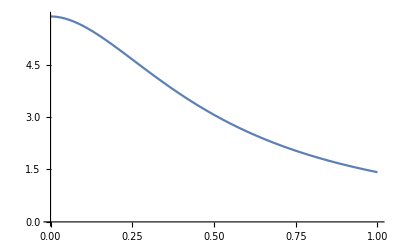

```mathematica
ListLinePlot[Table[{λdata[[i]],ηvec[[i]]},{i,1,NumGridPoints+1}]]
```

```mathematica
(* Export solutions, include Chebyshev grid parameters so we don't duplicate efforts *)
```

```mathematica
Export[NotebookDirectory[]<>"Data/probe_background_4d_sols_increasedAccuracy.mx",{μsind,μind,Q,λdata,D0λ,D1λ,D2λ,ϕvec,Axvec,ηvec}];
```

### Quasinormal mode via Newton-Raphson. Want to track superfluid second sound.

```mathematica
(* We will now scan a larger set of wavevectors zooming in on a single mode. *)
```

#### Numerical Parameters

```mathematica
(* If we start here, useful to redefine parameters for the numerics. Start with precision *)
```

```mathematica
mp=60;
$MinPrecision=mp;
```

```mathematica
(* Set threshold for "0" < 10^-mp *)
```

```mathematica
chopmin=10^-100;
```

```mathematica
(* Import higher accuracy background *)
```

```mathematica
{μsind,μind,Q,λdata,D0λ,D1λ,D2λ,ϕvec,Axvec,ηvec}=Import[NotebookDirectory[]<>"Data/probe_background_4d_sols_increasedAccuracy.mx"];
```

```mathematica
kmin = ktabLowPrec[[1]];
kmax = 10^2 kmin;
Numk = 10;
ktab = N[Table[kmin*10^(2 j/Numk),{j,0,Numk}],mp];
```

```mathematica
ωtab= Table[0,{i,1, Numk+1}];
```

#### Initialize EQs

```mathematica
Clear[kk]
```

```mathematica
(* We promote ω->ω[z]*)
```

```mathematica
fieldredefa=
{η[z]->z^2*η[z],ϕ[z]->ϕ[z](1-z),f[z]->1-z^3,σr[z]->z σr[z],σi[z]->z σi[z],at[z]->at[z](1-z)};
fieldredef=Flatten[{fieldredefa,D[fieldredefa,z],D[fieldredefa,{z,2}],ω->ω[z]}];
Clear[fieldredefa]
```

```mathematica
linearizedEQs = Import[NotebookDirectory[]<>"EQs/probe_4d_ingoingEQs.mx"]/.fieldredef//Expand//Simplify;
Clear[fieldredef]
```

```mathematica
(* Check scaling near boundaries *)
```

```mathematica
Series[linearizedEQs,{z,0,-1}]//Simplify
Series[linearizedEQs/.{z->1-z},{z,0,-1}]//Simplify
```

{O[z]^4,O[z]^4,O[z]^3,O[z]^3,O[z]^4}

{O[z]^2,O[z]^3,O[z]^3,O[z]^3,O[z]^1}

```mathematica
EQs=Simplify[Expand[({linearizedEQs[[1]]/((-1+z)^2 z^4),linearizedEQs[[2]]/(z^4(-1+z)^3),linearizedEQs[[3]]/(z^3(-1+z)^3),linearizedEQs[[4]]/(z^3(-1+z)^3),ω'[z]})]]//Simplify;
```

```mathematica
gaugeconstraint=Expand[linearizedEQs[[5]]/(z^4(-1+z))];
```

```mathematica
UVgaugeconstraint = gaugeconstraint/.{z->0}//Simplify;
IRgaugeconstraint =1/ω[1] gaugeconstraint/.{z->1}//Simplify;
```

```mathematica
{bc1,bc2,bc3,bc4}=EQs[[1;;4]]/.{z->1}//Simplify;
```

```mathematica
(* When we promote ω -> ω[z], it is important to fix a normalization for the fluctuations. We will choose them to match the sum from the direct eigensolver, call it horcon. *)
```

```mathematica
BCs = {{kk*at[zmin]+ω[zmin] ax[zmin],bc1},{UVgaugeconstraint,bc2},{σr[zmin],bc3},{σi[zmin],bc4},{ω'[zmin],at[zmax]+ax[zmax]+σr[zmax]+σi[zmax]-horcon}}//Simplify;
```

#### Linearize EQs

```mathematica
(* linearize the fields. *)
```

```mathematica
fieldRep = {at->at+ϵs*δat,ax->ax+ϵs*δax,σr->σr+ϵs*δσr,σi->σi+ϵs*δσi,ω->ω+ϵs*δω};
linBackEQ = D[(EQs/.fieldRep), ϵs]/.ϵs->0;
linBackBC= D[(BCs/.fieldRep), ϵs]/.ϵs->0;
Clear[fieldRep];

linFieldList = {δat[z],δax[z],δσr[z],δσi[z],δω[z]};
(*dlinFieldList⟦choose a function⟧⟦choose a derivative⟧*)
dlinFieldList= Table[{D[linFieldList[[fun]], z,z],D[linFieldList[[fun]], z],linFieldList[[fun]]},{fun,1,Length[linFieldList]}];
Clear[linFieldList]
(* must change argument for boundary conditions from z to zmin or zmax *)
boundrules= {z->zmin,z->zmax};
Do[linEQcoeffs[eq,fun,der] =D[linBackEQ⟦eq⟧,dlinFieldList⟦fun⟧⟦der⟧],{eq,1,Length[EQs]},{fun,1,Length[EQs]},{der,1,Length[dlinFieldList[[eq]]]}];
(*BCc⟦BC_i⟧⟦min or max⟧⟦choose a function⟧⟦derivative⟧*)
Do[linBCcoeffs[eq,bound,fun,der] =D[linBackBC⟦eq⟧⟦bound⟧, (dlinFieldList⟦fun⟧⟦der⟧/.boundrules⟦bound⟧)],{eq,1,Length[EQs]},{bound,1,2},{fun,1,Length[EQs]},{der,1,Length[dlinFieldList[[eq]]]}];
```

```mathematica
Clear[linBackBC,linBackEQ,dlinFieldList,boundrules]
```

#### Seeds for eigenvalue problem

```mathematica
(* The velocity of the superfluid sound mode is bounded above and below by 1 so let's try and find this eigenvalue. Furthermore, if we are in a stable regime, Im[ω]<0 but Im[ω/k^2] is not too negative for the hydrodynamic modes. In Eigensystem, eigenvalues are listed first and eigenvectors are listed second. For us, eigs[[wavevectorindex, 1 for eigenvalue or 2 for eigenvector, which eigenvalue]]. We expect a pair of modes. *)
```

```mathematica
hydroindex=Table[Position[Table[Abs[Re[eigsLowPrec[[j,1,i]]]]/ktabLowPrec[[j]]<1 && -10<Im[eigsLowPrec[[j,1,i]]]/ktabLowPrec[[j]]^2<0,{i,1,Length[eigsLowPrec[[j,1]]]}],True],{j,1,Length[ktabLowPrec]}];
```

```mathematica
hydroindex
```

{{{324},{325},{327}},{{324},{325},{327}}}

```mathematica
(* For the coarse grid with N=40, we see a mode at index 324 or 325 which satisfies the hydrodynamic criteria for our values of k. We use one of these as our seed. *)
```

```mathematica
ωseed = Table[eigsLowPrec[[1,1,hydroindex[[1,1,1]]]],{i,1,NumGridPoints+1}];
Export[NotebookDirectory[]<>"Data/probe_omegaseed_4d.mx",{ωseed[[1]],ktab[[1]]}];
```

```mathematica
(* Now, recall the eigenvectors have length 2*(number of fields)*(number of low precision grid points). The 2 is from ωδX and δX. We want just the fields over the grids so must partition. The number of fluctuating fields is the number of equations - 1 because we have included ω'[z] as an equation. *)
```

```mathematica
eigenfields = Partition[Partition[eigsLowPrec[[1,2,hydroindex[[1,1,1]]]],(Length[EQs]-1)*(Length[λdataLowPrec])][[2]],Length[λdataLowPrec]];
eigenfields2 = Partition[Partition[eigsLowPrec[[1,2,hydroindex[[1,1,1]]]],(Length[EQs]-1)*(Length[λdataLowPrec])][[1]],Length[λdataLowPrec]];
```

```mathematica
(* Check that eigenfields2 = ω*eigenfields1 *)
```

```mathematica
Table[Max[Chop[eigenfields2[[j]]-ωseed[[1]]*eigenfields[[j]]]],{j,1,4}]
```

{0,0,0,0}

```mathematica
(* The order of the fields follows from the above linearization step with linFieldList. It is at, ax, σr, then σi. *)
```

```mathematica
(* First interpolate *)
atint = Interpolation[Table[{λdataLowPrec[[i]],eigenfields[[1,i]]},{i,1,Length[λdataLowPrec]}]];
axint = Interpolation[Table[{λdataLowPrec[[i]],eigenfields[[2,i]]},{i,1,Length[λdataLowPrec]}]];
σrint = Interpolation[Table[{λdataLowPrec[[i]],eigenfields[[3,i]]},{i,1,Length[λdataLowPrec]}]];
σiint = Interpolation[Table[{λdataLowPrec[[i]],eigenfields[[4,i]]},{i,1,Length[λdataLowPrec]}]];
```

```mathematica
(* Now make the seeds. Importantly, we have to rescale to impose our boundary condition at the horizon. *)
```

```mathematica
horcon =Sum[eigenfields[[j,Length[λdataLowPrec]]],{j,1,4}];
```

```mathematica
horcon
```

-0.129100852984916706048120681023023817643980002844371657802196+0.00379969064776502399501435581479130617880182712406576007484155 ⅈ

```mathematica
atseed=Table[atint[λdata[[i]]],{i,1,NumGridPoints+1}];
axseed=Table[axint[λdata[[i]]],{i,1,NumGridPoints+1}];
σrseed=Table[σrint[λdata[[i]]],{i,1,NumGridPoints+1}];
σiseed=Table[σiint[λdata[[i]]],{i,1,NumGridPoints+1}];
```

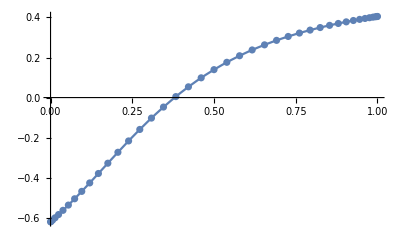
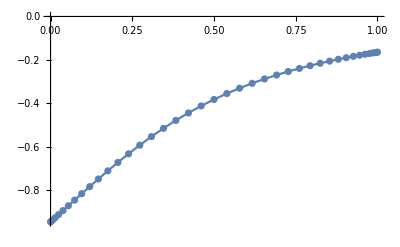
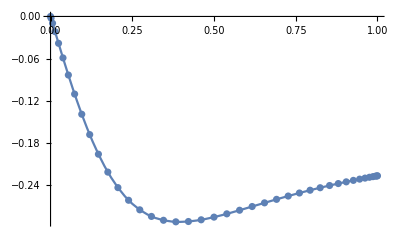
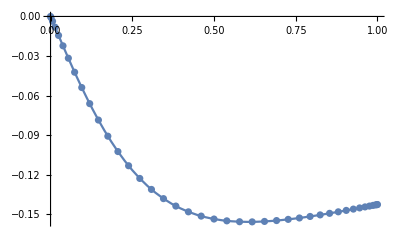

```mathematica
{Show[ListLinePlot[Table[{λdata[[i]],Re[atseed[[i]]]},{i,1,NumGridPoints+1}]],ListPlot[Table[{λdataLowPrec[[i]],Re[eigenfields[[1,i]]]},{i,1,Length[λdataLowPrec]}]]],
Show[ListLinePlot[Table[{λdata[[i]],Re[axseed[[i]]]},{i,1,NumGridPoints+1}]],ListPlot[Table[{λdataLowPrec[[i]],Re[eigenfields[[2,i]]]},{i,1,Length[λdataLowPrec]}]]],
Show[ListLinePlot[Table[{λdata[[i]],Re[σrseed[[i]]]},{i,1,NumGridPoints+1}]],ListPlot[Table[{λdataLowPrec[[i]],Re[eigenfields[[3,i]]]},{i,1,Length[λdataLowPrec]}]]],
Show[ListLinePlot[Table[{λdata[[i]],Re[σiseed[[i]]]},{i,1,NumGridPoints+1}]],ListPlot[Table[{λdataLowPrec[[i]],Re[eigenfields[[4,i]]]},{i,1,Length[λdataLowPrec]}]]]}
```

```mathematica
{atvec,axvec,σrvec,σivec,ωvec}={atseed,axseed,σrseed,σiseed,ωseed};
```

```mathematica
combinedFields=Flatten[{atvec,axvec,σrvec,σivec,ωvec}];
```

#### Find eigenvalues

```mathematica
nb=CreateDocument["",WindowSize->{Scaled[1/5],Scaled[1/2]}];

kcount = 1;

While[kcount≤Numk+1,

ϵp = (ErrorMax-Error)/2;
count = 0;

NotebookWrite[nb,Cell[BoxData@RowBox[{"kcount = ", kcount," timing = ",Timing[

While[ϵp>Error&&ϵp<ErrorMax,

μ=μtab[[μind]];
μs=μstab[[μsind]];
kk=ktab[[kcount]];


Do[coeffargs[i] = {z->λdata⟦i⟧,
ϕ''[z]->D2λ⟦i⟧.ϕvec,ϕ'[z]->D1λ⟦i⟧.ϕvec,ϕ[z]->ϕvec⟦i⟧,
Ax''[z]->D2λ⟦i⟧.Axvec,Ax'[z]->D1λ⟦i⟧.Axvec,Ax[z]->Axvec⟦i⟧,
η''[z]->D2λ⟦i⟧.ηvec,η'[z]->D1λ⟦i⟧.ηvec,η[z]->ηvec⟦i⟧,

at''[z]->D2λ⟦i⟧.atvec,at'[z]->D1λ⟦i⟧.atvec,at[z]->atvec⟦i⟧,
ax''[z]->D2λ⟦i⟧.axvec,ax'[z]->D1λ⟦i⟧.axvec,ax[z]->axvec⟦i⟧,
σr''[z]->D2λ⟦i⟧.σrvec,σr'[z]->D1λ⟦i⟧.σrvec,σr[z]->σrvec⟦i⟧,
σi''[z]->D2λ⟦i⟧.σivec,σi'[z]->D1λ⟦i⟧.σivec,σi[z]->σivec⟦i⟧,
ω''[z]->D2λ⟦i⟧.ωvec,ω'[z]->D1λ⟦i⟧.ωvec,ω[z]->ωvec⟦i⟧
},{i,1,NumGridPoints+1}];


(* Construct the derivative matrix *)
M =ArrayFlatten[Table[Sum[Flatten[Table[Piecewise[{{linBCcoeffs[m,1,n,dd]/.(coeffargs[1]/.{z->zmin}),i==1},
{linBCcoeffs[m,2,n,dd]/.(coeffargs[NumGridPoints+1]/.{z->zmax}),i==NumGridPoints+1},{linEQcoeffs[m,n,dd]/.coeffargs[i],i≠1&&i≠NumGridPoints+1}}],{i,1,NumGridPoints+1}]]Drmatrices[[dd]],{dd,1,Length[Drmatrices]}],{m,1,Length[EQs]},{n,1,Length[EQs]}]];

(* Construct the value of the eoms given the current configuration of the fields. *)
Etot =Chop[Flatten[Parallelize[Table[Piecewise[{{BCs[[m,1]]/.(coeffargs[1]/.{z->zmin}),i==1},{BCs[[m,2]]/.(coeffargs[NumGridPoints+1]/.{z->zmax}),i==NumGridPoints+1},{EQs[[m]]/.coeffargs[i],i≠1&&i≠NumGridPoints+1}}],
{m,1,Length[EQs]},{i,1,NumGridPoints+1}]]],chopmin];

(* Solve for the change in the fields *)
deltaFields=Chop[LinearSolve[M,-Etot],chopmin];

(* Compute the norm of deltaFields to keep track of convergence *)
ϵp=Norm[deltaFields,∞];

If[NumberQ[ϵp],NotebookWrite[nb,Cell[BoxData@RowBox[{"ϵp= ",ϵp}],"Output"]],Break[]];

(* If the norm is too large, introduce friction. *)
friction=If[ϵp<1,1,1/10];

combinedFields =combinedFields+friction*deltaFields;
(* partition the solution for the combined fields into individual fields *)
{atvec,axvec,σrvec,σivec,ωvec}= Partition[combinedFields,NumGridPoints+1];

Clear[friction,deltaFields];

count++;

];

]⟦1⟧,", # Iteration = ", count}],"Output"]];

ωtab[[kcount]]= ωvec[[1]];
kcount++;
];
NotebookClose[nb];
```

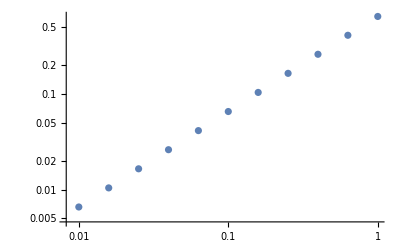

```mathematica
ListLogLogPlot[Table[{ktab[[i]],Abs[Re[ωtab[[i]]]]},{i,1,Numk+1}]]
```

```mathematica
(* Show that this is linear, i.e. a sound mode ω(k) ~ v*k *)
```

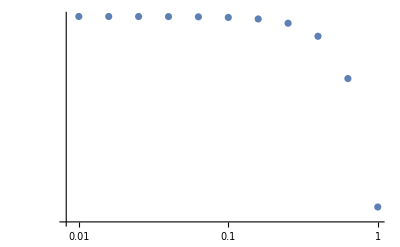

```mathematica
ListLogLogPlot[Table[{ktab[[i]],Abs[Re[ωtab[[i]]]]/ktab[[i]]},{i,1,Numk+1}]]
```

```mathematica
Export[NotebookDirectory[]<>"Data/probe_fluctuation_4d_sols_increasedAccuracy.mx",{μsind,μind,ktab,ωtab}];
```

## 5.) Matching to hydrodynamic theory

```mathematica
(* In appendix B of https://arxiv.org/pdf/2312.08243, I write the expression for the velocity of second sound in the probe limit (eq. B.3). Here we will just match the result to our numerics rather than deriving this expression. Since we only increased precision for one point, we will use the lower precision data for the thermodynamic derivatives. It is easy to change this by including more points when we increase precision.*)
```

```mathematica
Clear[μs,μ]
```

```mathematica
(* Define χξξ = μ/∂_ζ (Subscript[ζρ, s]) *)
```

```mathematica
χξξ[μs_,μ_,ρs_,χnsh_]:=μ/(μs*χnsh+ρs);
```

```mathematica
(* Define the velocity of second sound *)
```

```mathematica
velocityMinus[χnh_,χnn_,χξξ_]:=χnh/χnn-√(χnh^2/χnn^2+1/(χnn χξξ));
```

```mathematica
(* Construct thermodynamic derivatives *)
```

```mathematica
{Q,λdataLowPrec,D0λLowPrec,D1λLowPrec,D2λLowPrec,μtab,μstab,ϕvectabLowPrec,AxvectabLowPrec,ηvectabLowPrec}=Import[NotebookDirectory[]<>"Data/probe_background_4d_sols.mx"];
```

```mathematica
Nμ=Length[μtab]-1;
Nμs = Length[μstab]-1;
```

```mathematica
aμ=N[Table[Product[If[j==k,1,(μtab⟦j⟧-μtab⟦k⟧)],{k,1,Nμ+1}],{j,Nμ+1}],mp];
D1μ=Table[If[i==j,Sum[If[k==j,0,1/(μtab⟦j⟧-μtab⟦k⟧)],{k,1,Nμ+1}],aμ⟦i⟧/(aμ⟦j⟧(μtab⟦i⟧-μtab⟦j⟧))],{i,1,Nμ+1},{j,1,Nμ+1}];
Clear[aμ];
```

```mathematica
aμs=N[Table[Product[If[j==k,1,(μstab⟦j⟧-μstab⟦k⟧)],{k,1,Nμs+1}],{j,Nμs+1}],mp];
D1μs=Table[If[i==j,Sum[If[k==j,0,1/(μstab⟦j⟧-μstab⟦k⟧)],{k,1,Nμs+1}],aμs⟦i⟧/(aμs⟦j⟧(μstab⟦i⟧-μstab⟦j⟧))],{i,1,Nμs+1},{j,1,Nμs+1}];
Clear[aμs];
```

```mathematica
(* Calculate the order parameter, charge density, and supercurrent density*)
Otab=Table[ηvectabLowPrec[[i,j,1]],{i,1,Nμs+1},{j,1,Nμ+1}];
ρtab=Table[-D1λLowPrec[[1]].ϕvectabLowPrec[[i,j]]+ϕvectabLowPrec[[i,j,1]],{i,1,Nμs+1},{j,1,Nμ+1}];
Jxtab=Table[-D1λLowPrec[[1]].AxvectabLowPrec[[i,j]],{i,1,Nμs+1},{j,1,Nμ+1}];
ρstab=Table[μtab[[j]]/μstab[[i]] Jxtab[[i,j]],{i,1,Nμs+1},{j,1,Nμ+1}];
```

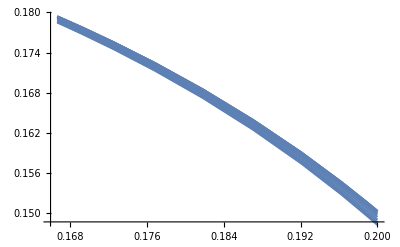

```mathematica
Show[Table[ListLinePlot[Table[{1/μtab[[j]],Otab[[i,j]]/μtab[[j]]^2},{j,1,Nμ+1}]],{i,1,Nμs+1}]]
```

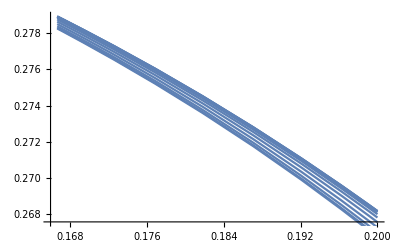

```mathematica
Show[Table[ListLinePlot[Table[{1/μtab[[j]],ρtab[[i,j]]/μtab[[j]]^2},{j,1,Nμ+1}]],{i,1,Nμs+1}]]
```

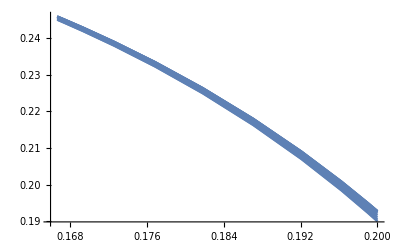

```mathematica
Show[Table[ListLinePlot[Table[{1/μtab[[j]],ρstab[[i,j]]/μtab[[j]]^2},{j,1,Nμ+1}]],{i,1,Nμs+1}]]
```

```mathematica
dρdζ=D1μs.ρtab;
dρdμ=Table[D1μ[[j]].ρtab[[i]],{i,1,Nμs+1},{j,1,Nμ+1}];
dρsdζ=D1μs.ρstab;
```

```mathematica
velocityTab=Table[velocityMinus[dρdζ[[i,j]],dρdμ[[i,j]],χξξ[μstab[[i]],μtab[[j]],ρstab[[i,j]],dρsdζ[[i,j]]]],{i,1,Nμs+1},{j,1,Nμ+1}];
```

```mathematica
(* Plot velocities. The red dot is where we look at the velocity*)
```

```mathematica
{ωcheck,kcheck}=Import[NotebookDirectory[]<>"Data/probe_omegaseed_4d.mx"];
```

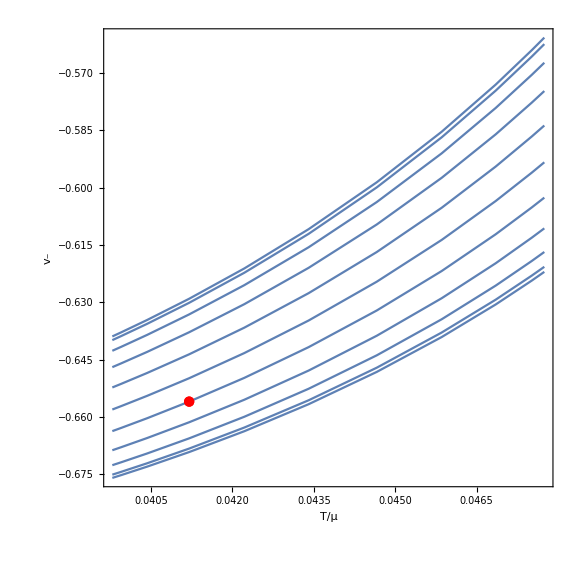

```mathematica
Show[Table[ListLinePlot[Table[{3/(4π μtab[[j]]),velocityTab[[i,j]]},{j,1,Nμ+1}],PlotRange->All],{i,1,Nμs+1}],ListPlot[{{3/(4π μtab[[μind]]),Re[ωcheck/kcheck]}},PlotStyle->Red],PlotRange->All,Frame->True,Axes->False,AspectRatio->1,FrameLabel->{{"v_-",""},{"T/μ",""}},RotateLabel->False,BaseStyle->{FontSize->22},ImageSize->Large]
```

```mathematica
velocityTab[[μsind,μind]]
```

-0.655998956186536502845012096669952750391312256977564128187941

```mathematica
Re[ωcheck/kcheck]
```

-0.655998634310152763995544284255483129790086710832858677329209

```mathematica
Im[ωcheck/kcheck^2]
```

-0.0284500844664581646848706393651982598002923915234086331998859

```mathematica
(* matches to 6 significant figures. The discrepancy is both numerical and from finite k effects. *)
```